```mathematica
G[u_,v_,J_,K_]:= (2 u K)/(v-u +v J +u K+√((v-u+v J+u K)^2-4(v-u)u  K))(*Goldbeter-Koshland Function*)
```

```mathematica
sys1:= D[R[t],t]== k0  G[k3 R[t],k4 ,J3,J4]+k1 S - k2  R[t](*pde*)
parameter:= {k0-> 0.4,k1-> 0.01 ,k2-> 1, k3->1 , k4-> 0.2, J3-> 0.05, J4-> 0.05}(**parameters)
```

```mathematica
b1=Solve[sys1[[2]]==0/.parameter,R[t]];(*nullclines*)
```

Global`b1

```mathematica
p1=Plot[Evaluate[{R[t]/.b1[[1]]}],{S,-15,15},PlotRange->{{0,15},{0,1}},PlotRangeClipping->True,Frame->True,PlotStyle->{Dashed}];

p2=Plot[Evaluate[{R[t]/.b1[[2]]}],{S,-15,15},PlotRange->{{0,15},{0,1}},PlotRangeClipping->True,Frame->True];
p3=Plot[Evaluate[{R[t]/.b1[[3]]}],{S,-15,15},PlotRange->{{0,15},{0,1}},PlotRangeClipping->True,Frame->True];
```

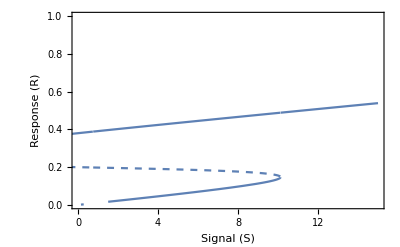

```mathematica
Show[{p1,p2,p3},FrameLabel->{"Signal (S)","Response (R)"},LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
List@@sys1[[2]];(*pde as a list*)
```

```mathematica
tmp1 = Cases[List@@sys1[[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]];(*sperating element with negative sigh*)
```

```mathematica
deg2 = - Plus@@tmp1;(*making a function*)
```

```mathematica
prod2 = Plus@@Complement[List@@sys1[[2]],tmp1](*positive part*)
```

k1 S+(2 J4 k0 k3 R[t])/(k4+J3 k4-k3 R[t]+J4 k3 R[t]+√(-4 J4 k3 R[t] (k4-k3 R[t])+(k4+J3 k4-k3 R[t]+J4 k3 R[t])^2))

```mathematica
Plot[{(prod2 /. parameter) /. S->0,(prod2 /. parameter) /. S->8,(prod2 /. parameter) /. S->16, deg2 /. parameter},{R[t],0,1},Frame->True,PlotRange->{{0,0.7},{0,0.6}},PlotRangeClipping->True, PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},Black},FrameLabel->{"R","Rate"},LabelStyle->{GrayLevel[0],Bold}]
```